```mathematica
FabiusF::usage="FabiusF[x] gives the value of the Fabius function F(x) for a non-negative real argument x.";
Macros`SetArgumentCount[FabiusF,1];
SyntaxInformation[FabiusF]={"ArgumentsPattern"->{_}};
SetAttributes[FabiusF,{NumericFunction,Listable}];
Derivative[n_Integer][FabiusF]:=2^(n (n+1)/2) FabiusF[2^n #]&
(*https://mathematica.stackexchange.com/a/13245*)
powerOfTwoQ[n_]:=IntegerQ[n]&&BitAnd[n,n-1]==0
FabiusF[Infinity]=Interval[{-1,1}];
FabiusF[x_?NumberQ]/;If[0≤Re[x]&&Im[x]==0,powerOfTwoQ[Denominator[x]],Message[FabiusF::realnn,x];False]:=iFabiusF[x]
ariasD[0]=1;
ariasD[n_Integer?Positive]:=ariasD[n]=Sum[2^((k (k-1)-n (n-1))/2) ariasD[k]/(n-k+1)!,{k,0,n-1}]/(2^n-1);
tri[x_]:=Piecewise[{{2-x,x>1}},x]
iFabiusF[x_]:=Module[{prec=Precision[x],s=1,y=0,z=SetPrecision[x,Infinity],n,p,q,tol,w},z=If[0≤z≤2,tri[z],q=Quotient[z,2];
(*can replace ThueMorse[] with the implementation in https://mathematica.stackexchange.com/a/89351*)If[ThueMorse[q]==1,s=-1];tri[z-2 q]];
tol=10^(-prec);
While[z>0,n=-Floor[RealExponent[z,2]];p=2^n;z-=1/p;w=1;
Do[w=ariasD[m]+p z w/(n-m+1);p/=2,{m,n}];
y=w-y;
If[Abs[w]<Abs[y] tol,Break[]]];
SetPrecision[s Abs[y],prec]];
```

.5-.5*(-1)^FLOOR(X)+(-1)^FLOOR(X)/(1+E^((-1+MOD(X,1))^(-1)+MOD(X,1)^(-1)))
.5+.5*(-1)^FLOOR(X)*TANH(.5/(1.-1.*MOD(X,1.))-.5/MOD(X,1.))
.5+((-1)^FLOOR(X)*(.5-.25*SQRT(4.+4.*ARCTANH(1.-2.*MOD(X,1))^2)))/ARCTANH(1.-2.*MOD(X,1))
.5-.5*(-1)^FLOOR(X)+(-1)^FLOOR(X)/(1+E^((-1+MOD(X,1))^(-1)+MOD(X,1)^(-1)))
.5+((-1)^FLOOR(X)*(1.-.5*SQRT(4+LOG(-1+MOD(X,1)^(-1))^2)))/LOG(-1+MOD(X,1)^(-1))
2*SQRT((-.5+(1+E^((-1.+MOD(.5+.5*X,1.))^(-1)+MOD(.5+.5*X,1.)^(-1)))^(-1))^2)
ABS((-2+SQRT(4+LOG(-1.+MOD(.5+.5*X,1.)^(-1))^2))/LOG(-1.+MOD(.5+.5*X,1.)^(-1)))/E^(PI*IM(FLOOR(.5+.5*X)))

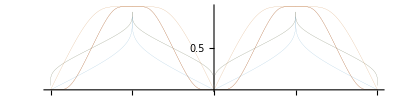

```mathematica
ᔓᔕ={(*WorkingPrecision-> 16,*)MaxRecursion-> Infinity,PlotPoints-> 1+2^8,PlotRangePadding-> 1/256, PlotRange-> Full,Ticks-> {Range[-2,2,.5],Range[-2,2,.5]},AspectRatio-> 1/4,ImageSize-> Full,PlotStyle-> {Thickness[1/65536]}};
ꗳ[X_]:=Exp[-1/X]/(Exp[-1/X]+Exp[-1/(1-X)]);
ᑐᑕꗳᑐᑕ[X_]:=(-1)^Floor[X] (ꗳ[Mod[X,1]]-0.5)+0.5;
ꗳꗳ[X_]:=0.5(1.+Tanh[(0.5-X)/((-1+X) X)]);
ᑐᑕꗳꗳᑐᑕ[X_]:=(-1)^Floor[X] (ꗳꗳ[Mod[X,1]]-0.5)+0.5;
ꗳꗳꗳ[X_]:=(0.5 (1.+1. ArcTanh[1.-2. X]))/ArcTanh[1.-2. X]-(0.25 Sqrt[4.+4. ArcTanh[1.-2. X]^2])/ArcTanh[1.-2. X];
ᑐᑕꗳꗳꗳᑐᑕ[X_]:=(-1)^Floor[X] (ꗳꗳꗳ[Mod[X,1]]-0.5)+0.5;
ꗳꗳꗳꗳ[X_]:=(1+E^((-1+X)^(-1)+X^(-1)))^(-1);
ᑐᑕꗳꗳꗳꗳᑐᑕ[X_]:=(-1)^Floor[X] (ꗳꗳꗳꗳ[Mod[X,1]]-0.5)+0.5;
ꗳꗳꗳꗳꗳ[X_]:=(2+Log[(1-X)/X]-Sqrt[4+Log[(1-X)/X]^2])/(2 Log[(1-X)/X]);
ᑐᑕꗳꗳꗳꗳꗳᑐᑕ[X_]:=(-1)^Floor[X] (ꗳꗳꗳꗳꗳ[Mod[X,1]]-0.5)+0.5;
ꗳꗳꗳꗳꗳꗳ[X_]:=(1+E^((-1+X)^(-1)+X^(-1)))^(-1);
ᑐᑕꗳꗳꗳꗳꗳꗳᑐᑕ[X_]:=Abs[(-1)^Floor[(X/2)+.5] (ꗳꗳꗳꗳꗳꗳ[Mod[(X/2)+.5,1]]-0.5)*2];
ꗳꗳꗳꗳꗳꗳꗳ[X_]:=(2+Log[-1+X^(-1)])/(2 Log[-1+X^(-1)])-Sqrt[4+Log[-1+X^(-1)]^2]/(2 Log[-1+X^(-1)]);
ᑐᑕꗳꗳꗳꗳꗳꗳꗳᑐᑕ[X_]:=Abs[(-1)^Floor[(X/2)+.5] (ꗳꗳꗳꗳꗳꗳꗳ[Mod[(X/2)+.5,1]]-0.5)*2];
(*Show[
Plot [ᑐᑕꗳꗳᑐᑕ[X],{X,-2,2},Evaluate[ᔓᔕ]]
,
Plot [ᑐᑕꗳꗳꗳᑐᑕ[X],{X,-2,2},Evaluate[ᔓᔕ]]
]*)
Column[{
ToUpperCase[StringReplace[ToString[FullSimplify[ExpandAll[ᑐᑕꗳᑐᑕ[X]]],InputForm],{"0."-> "."," "-> "","*^"-> "*10^","["->"(","]"->")"  }]],
ToUpperCase[StringReplace[ToString[FullSimplify[ExpandAll[ᑐᑕꗳꗳᑐᑕ[X]]],InputForm],{"0."-> "."," "-> "","*^"-> "*10^","["->"(","]"->")"  }]],
ToUpperCase[StringReplace[ToString[FullSimplify[ExpandAll[ᑐᑕꗳꗳꗳᑐᑕ[X]]],InputForm],{"0."-> "."," "-> "","*^"-> "*10^","["->"(","]"->")"  }]],
ToUpperCase[StringReplace[ToString[FullSimplify[ExpandAll[ᑐᑕꗳꗳꗳꗳᑐᑕ[X]]],InputForm],{"0."-> "."," "-> "","*^"-> "*10^","["->"(","]"->")"  }]],
ToUpperCase[StringReplace[ToString[FullSimplify[ExpandAll[ᑐᑕꗳꗳꗳꗳꗳᑐᑕ[X]]],InputForm],{"0."-> "."," "-> "","*^"-> "*10^","["->"(","]"->")"  }]],
ToUpperCase[StringReplace[ToString[FullSimplify[ComplexExpand[ᑐᑕꗳꗳꗳꗳꗳꗳᑐᑕ[X]]],InputForm],{"0."-> "."," "-> "","*^"-> "*10^","["->"(","]"->")"  }]],
ToUpperCase[StringReplace[ToString[FullSimplify[ExpandAll[ᑐᑕꗳꗳꗳꗳꗳꗳꗳᑐᑕ[X]]],InputForm],{"0."-> "."," "-> "","*^"-> "*10^","["->"(","]"->")"  }]]
}]
Plot [{ᑐᑕꗳᑐᑕ[X],ᑐᑕꗳꗳᑐᑕ[X],ᑐᑕꗳꗳꗳᑐᑕ[X],ᑐᑕꗳꗳꗳꗳᑐᑕ[X],ᑐᑕꗳꗳꗳꗳꗳᑐᑕ[X],ᑐᑕꗳꗳꗳꗳꗳꗳᑐᑕ[X],ᑐᑕꗳꗳꗳꗳꗳꗳꗳᑐᑕ[X]},{X,-2,2},Evaluate[ᔓᔕ],PlotLegends-> Placed["Expressions",{Center,Top}],LabelStyle->Directive[FontFamily->"Arial",GrayLevel[134/256],FontSize->12]]
```